# DMDGP Package

```mathematica
(* Aborting after first error - Put the following two lines at the top of every notebook. *)
(* messageHandler=If[Last[#],Abort[]]&;
Internal`AddHandler["Message",messageHandler]; *)
```

## Basic Routines, Instance Creation, LDME and RMSD

### Source Code: Instance Creation and Basic Routines

```mathematica
ClearAll[
SetPositionUsingCartesianSystem,
SetPositionUsingHomogeneousCoords,
CalculateProteinAngles,
CalculateTorsionAngles,
GenerateRandom3DBackbone,
GenerateRandomMDGP,
GetMatrixDistance,
Plot3DBackbone,
WriteMDGP
];

GetEdgeWeight::usage="Gets edge weight. 'E' can be a single edge or a list of edges.";
GetEdgeWeight[G_,E_]:=Module[
{i,D={}},
If[Not[FailureQ[PropertyValue[{G,E[[1]]},EdgeWeight]]],
(* E is a list of edges *)
For[i=1,i≤Length[E],i++,AppendTo[D,PropertyValue[{G,E[[i]]},EdgeWeight]]],
(* E is a single edge *)
D=PropertyValue[{G,E},EdgeWeight]
];
Return[D]
];
GetEdgeDistanceBounds[G_,E_]:=Module[
{Lij,Uij,Vij},
Vij=PropertyValue[{G,E},"DistanceBounds"];
Return[Vij]
];

SetPositionUsingCartesianSystem[d_,θ_,ω_]:=
(* Calculates Euclidean coords from distances, planar and dihedral angles using rotations and translations explicitly;
   Input parameters;
   d: distances       (d[i] = norm(x[[i]]-x[[i-1]]));            
   θ: planar angles   (θ[i] = angle(x[i],x[i-1],x[i-2]));        
   ω: dihedral angles (ω[i] = angle(x[i],x[i-1],x[i-2],x[i-3]) 
*)
Module[
(* declare local variables *)
{a,b,c,i,v,n,R,X,numberOfAtoms},
numberOfAtoms=Length[d];
(* atoms positions on Euclidean 3d space *)
X=Table[0,{i,numberOfAtoms},{j,3}];
(* set the position of the three first points *)
X[[{1,2,3}]]={{0,0,0},{-d[[2]],0,0},{-d[[2]]+d[[3]]Cos[θ[[3]]],d[[3]]Sin[θ[[3]]] ,0}};
(* set remaining positions *)
For[i=4,i≤numberOfAtoms,i++,
{a,b,c}={X[[i-3]],X[[i-2]],X[[i-1]]};
v= d[[i]]* Normalize[b-c]; 
(* normal to the plane abc *)
n=Cross[a-b,c-b];
(* apply plane rotation *)
R=RotationTransform[θ[[i]],n]; (* rotation creation *)
v=R[v]; (* rotation apply *)
(* apply torsion rotation and translation *)
R=RotationTransform[ω[[i]],c-b];
v=R[v]+c;
(* set i-th coordinate *)
X[[i]]=v
];
Return[X]
];

SetPositionUsingHomogeneousCoords::usage="Set the atoms positions using internal coordinate system.";
SetPositionUsingHomogeneousCoords[d_,θ_,ω_]:=
(* Calculates Euclidean coords from distances, planar and dihedral angles using transformation matrices;
   Input parameters;
   d: distances       (d[i] = norm(x[[i]]-x[[i-1]]));            
   θ: planar angles   (θ[i] = angle(x[i],x[i-1],x[i-2]));        
   ω: dihedral angles (ω[i] = angle(x[i],x[i-1],x[i-2],x[i-3]); 
*)
Module[
{B,B1,B2,B3,X,i,di,ct,st,cw,sw,v,numberOfAtoms},
numberOfAtoms=Length[d];
(* atoms positions on Euclidean 3d space *)
X=Table[0,{i,numberOfAtoms},{j,3}];
(* set the position of the three first points *)
{ct,st}={Cos[θ[[3]]],Sin[θ[[3]]]};
X[[{1,2,3}]]={{0,0,0},{-d[[2]],0,0},{-d[[2]]+d[[3]]ct,d[[3]]st ,0}};
(* set first transformation matrices *)
B1=IdentityMatrix[4];
B2={{-1,0,0,-d[[2]]},{0,1,0,0},{0,0,-1,0},{0,0,0,1}};
di=d[[3]];
B3={{-ct,-st,0,-di*ct},{st,-ct,0,di*st},{0,0,1,0},{0,0,0,1}};
(* set remaining coordinates *)
B=B1.B2.B3;
For[i=4,i≤numberOfAtoms,i++,
{ct,st}={Cos[θ[[i]]],Sin[θ[[i]]]};
{cw,sw}={Cos[ω[[i]]],Sin[ω[[i]]]};
di=d[[i]];
(* concatenate transformation matrices *)
B =B.{{-ct,-st,0,-di*ct},{st*cw,-ct*cw,-sw,di*st*cw},{st*sw,-ct*sw,cw,di*st*sw},{0,0,0,1}};
(* apply transformation at origin *)
v =B.{0,0,0,1};
(* update coordinate *)
X[[i]]=v[[{1,2,3}]];
];
Return[X]
];

GenerateRandom3DBackbone[numberOfAtoms_,algorithm_:"HomogeneousCoords",seed_:0]:=
(* Generates a random backbone in tridimensional Euclidean space;
   Input parameters;
   numberOfAtoms: number of 3D Euclidean points to be generated;
   algorithm: algorithm to be applied during coordinates calculation. The options 'are HomogeneousCoords' or 'CartesianSystem';
   seed: integer number used to reproduce random sequence generation. If seed=0 a sequence based on the current time is constructed;
 *)
Module[
(* declare the local variables *)
{d,θ,ω,X,output,ϵ=0.05},
(* set seed *)
If[seed>0,SeedRandom[seed]];
(* length of covalent bonds *)
d=Table[1.526,{i,numberOfAtoms}];
d[[1]]=0;
(* plane angles *)
θ=Table[1.91,{i,numberOfAtoms}];
θ[[{1,2}]]={0,0};
(* torsion angles *)
ω=Table[RandomChoice[{60Degree,180Degree,300Degree}]*(1+RandomReal[{-ϵ,ϵ}]),{i,numberOfAtoms}];
ω[[{1,2,3}]]={0,0,0};
(* set the remaining 3d positions *)
Switch[algorithm,
"HomogeneousCoords",X=SetPositionUsingHomogeneousCoords[d,θ,ω],
"CartesianSystem",X=SetPositionUsingCartesianSystem[d,θ,ω],
_,Throw["InvalidAlgorithm:",OptionValue[algorithm]]
];
(* set output *)
<|"Points"->X,"TorsionAngles"->ω,"CovalentBondLengths"->d,"PlaneRotationAngles"->θ|>
];

GetMatrixDistance[x_]:=
(* Calculates the complete distance matrix for all coordinates x[[i]] in the array x. *)
Table[Norm[x[[i]]-x[[j]]],{i,1,Length[x]},{j,1,Length[x]}];

GenerateRandomMDGP[numberOfAtoms_,dijMax_:5.0,dijPrec_:0.0,seed_:0]:=
(* Generates a random DMDGP instance.; 
   numberOfAtoms: number of 3D Euclidean points to be generated
dijMax: all distances greater than dijMax are dropped
dijPrec: the upper (uij) and lower (lij) constraints boundaries are 
generated using the formulae lij = (1-dijPrec) and uij = (1+dijPrec); 
   algorithm: defines the method (algorithm) used to calculate the pairwise
   distances. The options are "DistanceMatrix" and "Nearest";
   seed: integer number used to reproduce random sequence generation. If 
  seed=0 a sequence based on current is constructed;
*)
Module[
(* declare local variables *)
{i,j,k,X,G,D,N,E,dij},
X=GenerateRandom3DBackbone[numberOfAtoms,"HomogeneousCoords",seed];
D=DistanceMatrix[X["Points"]];
G=Table[If[And[0<D[[i]][[j]],D[[i]][[j]]≤dijMax],D[[i]][[j]],Infinity],{i,1,numberOfAtoms},{j,1,numberOfAtoms}];
G=WeightedAdjacencyGraph[G];
(* set distance bounds *)
E=EdgeList[G];
For[k=1,k≤Length[E],k++,
{i=E[[k]][[1]],j=E[[k]][[2]]};
dij=GetEdgeWeight[G,E[[k]]];
If[Abs[i-j]>2,
(* imprecise distance *)
PropertyValue[{G,i<->j},"DistanceBounds"]={(1-dijPrec),(1+dijPrec)}*dij,
(* exact distance *)
PropertyValue[{G,i<->j},"DistanceBounds"]={dij,dij}
];
];
Return[<|"X"->X,"G"->G|>]
];

CalculateProteinAngles[A_,B_,C_,D_]:=
(* Calculates the protein angles (plane and torsion) for 3D points A, B, C and D in that order. *)
Module[
(* Calculate the plane and torsion angles for X4 *)
{nabc, nbcd,θ,ω},
(* centered at C *)
θ=VectorAngle[B-C,D-C];
Print["(θ):Angle[BCD]  =",θ];
(* centered at B and C *)
{nabc,nbcd} = {Cross[A-B,C-B],Cross[B-C,D-C]};
ω=VectorAngle[nabc,nbcd];
Print["(ω):Angle[ABCD] =",ω];
Return[{θ,ω}];
];

CalculateProteinAnglesForAtomAtPosition[X_,i_]:=
(* Calculates the protein angles (plane and torsion) to i-th atom. *)
CalculateProteinAngles[X[[i-3]],X[[i-2]],X[[i-1]],X[[i]]];

CalculateTorsionAngles[X_]:=Module[
{θ,ω,i},
ω=Table[0,{i,1,Length[X]}];
For[i=4,i≤Length[X],i++,
{θ,ω[[i]]}=CalculateProteinAnglesForAtomAtPosition[X,i]
];
Return[ω]
];

IsNaturalOrderValid[G_]:=
(* Checks if the ordering assumption of DMDGP is satisfied by G edges *)
Module[
(* local variables *)
{i,j},
For[i=4,i≤Length[VertexList[G]],i++,
For[j=1,j≤3,j++,
If[FailureQ[GetEdgeWeight[G,(i-j)<->i]],
Print["The edge ",(i-j)<->i," is missing"];
Return[False]]];
];
Return[True]
];

CalculatePartialSolutionError[G_,X_,i_]:=
(* Calculates the error (constraints violation) on the substructure X[[1:i]] *)
Module[
(* local variables *)
{eij,j,k,V,Xi,Xj,Dij,Lij,Uij,errorDij},
(* current position *)
Xi=X[[i]];
(* considering only the precedent atoms *)
V= Select[AdjacencyList[G,i],#<i&];
(*Print["V=",V];*)
errorDij=0.0;
For[k=1,k≤Length[V],k++,
(* neighbor index *)
j=V[[k]]; 
(* neighbor coordinate *)
Xj=X[[j]];
(* actual distance *)
Dij=EuclideanDistance[Xi,Xj];
(* distance bounds *)
{Lij,Uij}=GetEdgeDistanceBounds[G,i<->j];
(* error Dij *)
eij=Max[(Lij-Dij)/Lij,(Dij-Uij)/Uij];
(* update error *)
If[eij>errorDij,
errorDij=eij;
(*Print["i=",i," j=",j," Lij=",Lij, " Uij=",Uij, " Dij=",Dij," eij=",errorDij];*)
];
];
Return[errorDij]
];

ApplyRotors[X_,ω_]:=Module[{i,j,Y},
Y=Table[X[[i]],{i,Length[X]}];
For[i=4,i≤Length[X],i++,
For[j=i,j≤Length[X],j++,
Y[[j]]=RotationTransform[ω[[i]],Y[[i-1]]-Y[[i-2]],Y[[i-1]]][Y[[j]]]
];
];
Return[Y]
];

WriteMDGP[M_,fname_]:=
(* Create the files fname.csv and fname_xsol.csv with, respectively, the MDGP constraints given by M["G"] and the associated solution M["X"] *)
Module[{edges,fid,table,eij,i,j,k,X,G,Lij,Uij},
X=M["X"]["Points"];
table=Table[X[[i]][[j]],{i,Length[X]},{j,3}];
fid=StringJoin["C:\\Users\\Michael\\gitrepos\\github\\bioinfo\\instances\\",fname,"_xsol.csv"];
Export[fid,table,TableHeadings->{"x","y","z"}];
G=M["G"];
edges=EdgeList[G];
table=Table[0,{i,Length[edges]},{j,4}];
For[k=1,k≤Length[edges],k++,
eij=edges[[k]];
{i,j}={eij[[1]],eij[[2]]};
{Lij,Uij}=GetEdgeDistanceBounds[G,eij];
table[[k]]={i,j,Lij,Uij}
];
fid=StringJoin["C:\\Users\\Michael\\gitrepos\\github\\bioinfo\\instances\\",fname,".csv"];
Export[fid,table,TableHeadings->{"I","J","L","U"}]
];

Plot3DBackbone[X_]:=
(* Plots the points using the coordinates of X["Points"] property *)
Graphics3D[{{Red,Tube[X]},{PointSize[Large],Blue,Point[Rest[X]]},{PointSize[Large],Green,Point[First[X]]}}, Axes->True]

PlotAdjacencyMatrix[G_,DiagonalCovering_:False]:=Module[
{i,j,n,ei,ej,edges,primitives,add},
n=Max[VertexList[G]];
edges=EdgeList[G];
(* inverting edges position *)
edges=Table[{edges[[i]][[2]],n-edges[[i]][[1]]+1},{i,Length[edges]}];
primitives={
{PointSize[Medium],Point[edges]},
{Red,Dashed,Line[{{1,n},{n,1}}]}
};
(* Plot diagonal covering *)
If[DiagonalCovering,
For[i=1,i≤Length[edges],i++,
add=True;
ei=edges[[i]];
For[j=1,j≤Length[edges],j++,
ej=edges[[j]];
If[(ej[[1]]==ei[[1]]&&ej[[2]]>ei[[2]]),add=False];
If[(ej[[2]]==ei[[2]]&&ej[[1]]>ei[[1]]),add=False];
];
If[add,
PrependTo[primitives,
{Opacity[0.2],Red,Triangle[{{ei[[1]],n+1-ei[[1]]},ei,{n+1-ei[[2]],ei[[2]]}}]}]
];
];
];
Graphics[primitives,
Axes->True,
GridLines->Automatic,
Ticks->{Automatic,Table[{i,n+1-i},{i,n}]},
AxesOrigin->{1,1}
]
];
```

### Source Code: LDME

```mathematica
LDME[G_,X_]:=Module[
{i,j,k,E,ldme=0,lij,uij,dij},
E=EdgeList[G];
For[k=1,k≤Length[E],k++,
{lij,uij}=GetEdgeDistanceBounds[G,E[[k]]];
i=E[[k]][[1]];
j=E[[k]][[2]];
dij=Norm[X[[i]]-X[[j]],2];
ldme+=Max[lij-dij,dij-uij,0]^2
];
Return[Sqrt[ldme/Length[E]]]
];
```

### Source Code: RMSD

```mathematica
RMSD[X_,Y_]:=Module[
{xc,yc,x,y,U,D,V,rmsd},
(* calculating centers *)
xc=Mean[X];
yc=Mean[Y];
(* translation *)
x=Table[X[[i]]-xc,{i,Length[X]}];
y=Table[Y[[i]]-yc,{i,Length[Y]}];
(* svd *)
V=Transpose[x].y;
{U,D,V}=SingularValueDecomposition[V];
V=U.Transpose[V];
x=x.V;
rmsd=Norm[x-y,"Frobenius"]/Sqrt[Length[x]];
Return[{rmsd,V,x,y}]
]
```

```mathematica
(* Example: X and Y are 5 x 3 matrix *)
X={{0.814700,0.097500,0.157600},{0.905800,0.278500,0.970600},{0.127000,0.546900,0.957200},{0.913400,0.957500,0.485400},{0.632400,0.964900,0.800300}};
Y={{6.167723,5.509229,5.376972},{5.921716,5.625914,6.161379},{5.265461,5.705450,6.339958},{5.936486,6.432611,5.883000},{5.680966,5.982123,5.893736}};
{MatrixForm[X],MatrixForm[Y]}
{rmsd,Q,x,y}=RMSD[X,Y]
{rmsd,MatrixForm[Q],MatrixForm[x],MatrixForm[y]}
```

### Source Code: Check MDGP Solution Quality

```mathematica
CheckMDGPSolutionQuality[G_,X_]:=Module[
{i,j,k,dij, Dij,numberOfEdges,E,error},
E=EdgeList[G];
numberOfEdges=Length[E];
error=Table[0,{i,numberOfEdges}];
For[k=1,k≤numberOfEdges,k++,
{i=E[[k]][[1]],j=E[[k]][[2]]};
dij=GetEdgeWeight[G,i<->j];
Dij=Norm[X[[i]]-X[[j]]];
error[[k]]=Abs[Dij-dij];
];
Print["max(error) = ",Max[error], " mean(error) = ", Mean[error]]
];
```

### Examples

#### Generating Random Backbone

```mathematica
X=GenerateRandom3DBackbone[8,algorithm="HomogeneousCoords"];
Print["X=",X];
Plot3DBackbone[X["Points"]]
```

#### Set Position Using Different Coordinate Systems

```mathematica
d=X["CovalentBondLengths"];
t=X["PlaneRotationAngles"];
w=X["TorsionAngles"];
S=SetPositionUsingCartesianSystem[d,t,w];
P=SetPositionUsingHomogeneousCoords[d,t,w];
Print["S=",S];
Print["P=",P];
CalculateProteinAnglesForAtomAtPosition[S,7];
CalculateProteinAnglesForAtomAtPosition[P,7];
```

#### Generate Random DMDGP Instance

ylabel={{1,8},{2,7},{3,6},{4,5},{5,4},{6,3},{7,2},{8,1}}

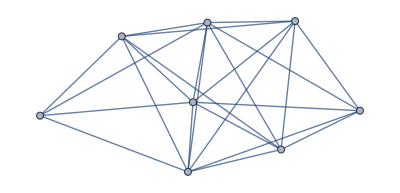
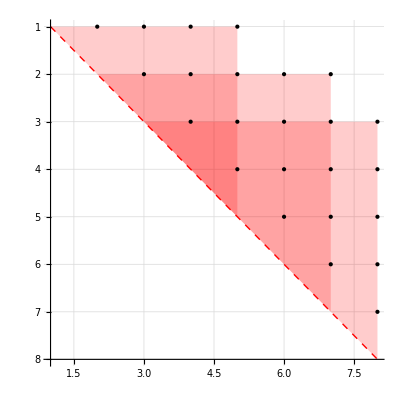
{-Graphics-,-Graphics-,-Graphics3D-}

```mathematica
ClearAll[M];
natoms =8;
dijMax=5;
dijPrec=0.1;
M=GenerateRandomMDGP[natoms,dijMax,dijPrec,seed=False];{G=M["G"],X=M["X"]};
{G,PlotAdjacencyMatrix[G,True], Plot3DBackbone[X["Points"]]}
(*WriteMDGP[M,StringJoin[{"dmdgp_N",ToString[natoms],"_D",ToString[dijMax],"_P",ToString[dijPrec],"_S",ToString[seed]}]]*)
```

#### Generate Random IMDGP Instance

```mathematica
ClearAll[M];
M=GenerateRandomMDGP[7,dtol=5,dprec=0.0,seed=1];{G=M["G"],X=M["X"]};
{G, Plot3DBackbone[X["Points"]]}
{Lij,Uij}=GetEdgeDistanceBounds[G,1<->4]
```

#### Creating Sample

```mathematica
ClearAll[GenerateSample3DBackbone]
GenerateSample3DBackbone[numberOfAtoms_,ω_]:=
Module[{i,k,d,w,θ,X,nvals,nsample,angle,scod,aid},
(* length of covalent bonds *)
d=Table[1.526,{i,numberOfAtoms}];
(* planar angles *)
θ=Table[1.91,{i,numberOfAtoms}];
(* torsion angles *)
w=Table[0,{i,numberOfAtoms}];
nvals=Length[ω];
nsample=nvals^(numberOfAtoms-3);
X=Table[{0,0,0},{i,nsample}];(* coordinates *)
For[k=0,k<nsample,k++,
scod=k; (* sample code *)
For[i=0,i<(numberOfAtoms-3),i++,
aid=Mod[scod,nvals];
scod=(scod-aid)/nvals;
w[[4+i]]=ω[[aid+1]]
];
X[[k+1]]=SetPositionUsingHomogeneousCoords[d,θ,w]
];
Return[X]
];
```

```mathematica
(* Attention: It takes a lot of time!!! *)
X=GenerateSample3DBackbone[8,Table[i*Pi/6,{i,11}]];
Length[X]
```

```mathematica
(* saving structures *)
Export["C:\\Users\\Michael\\gitrepos\\github\\bioinfo\\XCOORDS8.dat",X,"Table"];
```

#### Profiling (Timing)

```mathematica
(* Comparison between HomogeneousCoords and CartesianSystem algorithms *)
(*
Print["Time(HomogeneousCoords)=",First[Timing[Timing[GenerateRandom3DBackbone[1000,"HomogeneousCoords"]]]]];
Print["Time(CartesianSystem)=",First[Timing[Timing[GenerateRandom3DBackbone[1000,"CartesianSystem"]]]]];
*)
```

```mathematica
(* Estimating complexity of random backbone generation *)
(*
Clear[x];
tp=Table[{n,First[Timing[GenerateRandom3DBackbone[n,"HomogeneousCoords"]]]},{n,100,10000,100}];
fp=Fit[tp,{1,x},x];
Show[ListPlot[tp],Plot[{fp},{x,100,10000}],AxesLabel->{HoldForm[Problem Size],HoldForm[Time in Seconds]},PlotLabel->HoldForm[GenerateRandom3DBackbone],LabelStyle->{GrayLevel[0]}]
*)
```

```mathematica
(* Estimating complexity of distance calculation algorithms in GenerateRandomMDGP function *)
(*
numberOfAtoms=50
First[Timing[M=GenerateRandomMDGP[numberOfAtoms,Dtol=5.0]]]
*)
```

## Applying General Methods

### Source Code: Create MDGP instance from solution and pairs

```mathematica
MDGPAllPairs[n_]:=Module[{i,j,k=0,pij},
pij=Table[0,{i,(n(n-1))/2}];
For[i=1,i≤n,i++,
For[j=(i+1),j≤n,j++,
k++;
pij[[k]]={i,j};
];
];
Return[pij]
];
MDGPCreateInstanceFromSolutionAndPairs[x_,eij_]:=Module[{i,j,d,G},
i=Table[eij[[k]][[1]],{k,Length[eij]}];
j=Table[eij[[k]][[2]],{k,Length[eij]}];
d=Table[Norm[x[[i[[k]]]]-x[[j[[k]]]]],{k,Length[eij]}];
Return[{i,j,d}]
]
```

### Source Code : Check MDGP solution

```mathematica
CheckMDGPSolution[i_,j_,d_,x_,verbose_:True]:=Module[{k,f,G},
f=0;
For[k=1,k≤Length[i],k++,
(* sum of errors *)
f+=Abs[N[(d[[k]]-Norm[x[[i[[k]]]]-x[[j[[k]]]]])]];
];
If[verbose,
G=SparseArray[Table[{i[[k]],j[[k]]}->1,{k,Length[i]}]];
(*Print[MatrixPlot[G,ColorFunction->"LightTemperatureMap",ImageSize->Small,Mesh->All,MeshStyle->{Black,Dashed}]];*)
Print[MatrixForm[G,TableHeadings->{DeleteDuplicates[i],Table[k,{k,Length[x]}]}]];
Print["Checking solution:"];
Print["   Number of equations = ", Length[d]];
Print["   Number of points    = ", Length[x]];
Print["   Solution abs(error) = ", f];
];
Return[f];
]
```

### Source Code: Nonlinear equations

```mathematica
MDGPNSolve[i_,j_,d_]:=Module[{k,eqs,xi,xj,x,n},
eqs=Table[0,{k,Length[i]}];
n=Max[i,j];
x=Table[Symbol[StringJoin["x",ToString[xi],ToString[xj]]],{xi,n},{xj,3}];
For[k=1,k≤Length[i],k++,
xi=x[[i[[k]]]];
xj=x[[j[[k]]]];
eqs[[k]]=(xi[[1]]-xj[[1]])^2+(xi[[2]]-xj[[2]])^2+(xi[[3]]-xj[[3]])^2-d[[k]]^2
];
eqs=Join[eqs,{x[[1]][[1]]==0,x[[1]][[2]]==0,x[[1]][[3]]==0}];
(*Print["eqs=",eqs];*)
(*Print["x=",x];*)
x=Flatten[x];
(*x=Table[{x[[k]],RandomReal[]},{k,Length[x]}];
x=FindRoot[eqs,x];*)
Quiet[x=NSolve[eqs,x,Reals]];
x=ArrayReshape[x,{n,3}];
Print["x=",x];
Return[x]
];
```

```mathematica
(* Example: 5 points *)
eij={{1,2},{1,3},{2,3},{1,4},{2,5}};
x={{0,0,0},{1,0,0},{0,1,0},{0,0,1},{1,1,0}};
(*x=RandomReal[1,{5,3}];*)
{i,j,d}=MDGPCreateInstanceFromSolutionAndPairs[x,eij];
x=MDGPNSolve[i,j,d];
x=Table[x[[i]][[j]][[2]],{i,Length[x]},{j,3}];
MatrixForm[x]
CheckMDGPSolution[i,j,d,x,True];
```

```mathematica
CheckMDGPSolution[i,j,d,x,True];
```

```mathematica
CheckMDGPSolution[i,j,d,x,True];
```

```mathematica
(* Example: 10 points *)
n=5;
eij=MDGPAllPairs[n];
x=RandomReal[1,{n,3}];
{i,j,d}=MDGPCreateInstanceFromSolutionAndPairs[x,eij];
x=MDGPNSolve[i,j,d];
CheckMDGPSolution[i,j,d,x];
```

### Source Code: Solver for complete distance matrices

```mathematica
MDGPAllInstancesSolver[i_,j_,d_]:=Module[{numberOfAtoms,k,m,λ,v,x},
numberOfAtoms=Max[{i,j}];
(* creates distance matrix *)
m=Table[0,{iloc,numberOfAtoms},{jloc,numberOfAtoms}];
For[k=1,k≤Length[i],k++,
m[[i[[k]]]][[j[[k]]]]=d[[k]];
m[[j[[k]]]][[i[[k]]]]=d[[k]];
];
(* λ:eigenvalues and v:eigenvectors *)
m=Table[(m[[1]][[iloc]]^2+m[[1]][[jloc]]^2-m[[iloc]][[jloc]]^2)/2,{iloc,numberOfAtoms},{jloc,numberOfAtoms}];
{λ,v}=Eigensystem[m,3];
(* getting solution *)
x=Table[Sqrt[λ[[jloc]]]v[[jloc]][[iloc]],{iloc,numberOfAtoms},{jloc,3}];
Return[x]
]
```

### Source Code: Solver based on optimization methods

```mathematica
MDGPOptSolverFobj[i_,j_,d_,x_]:=Module[{f=0,numberOfAtoms,ncols,nrows,k,y},
y=ArrayReshape[x,{Length[x]/3,3}];
For[k=1,k≤Length[d],k++,
f+=(d[[k]]^2-Norm[y[[i[[k]]]]-y[[j[[k]]]]]^2)^2
];
Return[f]
]
MDGPOptSolver[i_,j_,d_]:=Module[{numberOfAtoms,f,y,v,w},
numberOfAtoms=Max[{i,j}];
ClearAll[z];
y=Array[z,3*numberOfAtoms];
f:=MDGPOptSolverFobj[i,j,d,#]&;
{v,y}=NMinimize[f[y],y];
y=ArrayReshape[y,{Length[y]/3,3}];
y=Table[y[[iloc]][[jloc]][[2]],{iloc,Length[y]},{jloc,3}];
Return[y]
]
```

### Examples

```mathematica
(* Example A: Solving an instance with 4 points and complete distance matrix *)
x={{0,0,0},{1,0,0},{0,1,0},{0,0,1}};
eij=MDGPAllPairs[Length[x]];
{i,j,d}=MDGPCreateInstanceFromSolutionAndPairs[x,eij];
y=MDGPAllInstancesSolver[i,j,d]
CheckMDGPSolution[i,j,d,y];
```

```mathematica
(* Example B: Solving an instance with 100 points and complete distance matrix *)
x=RandomReal[1,{100,3}];
eij=MDGPAllPairs[Length[x]];
{i,j,d}=MDGPCreateInstanceFromSolutionAndPairs[x,eij];
y=MDGPAllInstancesSolver[i,j,d];
CheckMDGPSolution[i,j,d,y];
```

```mathematica
(* Example C: Solving an instance with 5 points using optimization based method *)
x=RandomReal[1,{5,3}];
eij={{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{4,5}};
{i,j,d}=MDGPCreateInstanceFromSolutionAndPairs[x,eij];
y=MDGPOptSolver[i,j,d];
CheckMDGPSolution[i,j,d,y];
```

```mathematica
(* Example D: Solving an instance with 100 points using optimization based method *)
(* It can take a lot of time!!! *) 
(* For[k=1,k≤100,k++,
SeedRandom[k];
x=RandomReal[1,{7,3}];
eij=MDGPAllPairs[Length[x]];
eij=RandomSample[eij,Round[0.50Length[eij]]];
{i,j,d}=MDGPCreateInstanceFromSolutionAndPairs[x,eij];
y=MDGPOptSolver[i,j,d];
f=CheckMDGPSolution[i,j,d,y,False];
If[Or[f>0.01,Mod[k,10]==0],
Print["{Seed,Error}=",{k,f}];
];
]
*)
```

## Solving Manually: Continuos Problem

```mathematica
GetEuclideanCoords[θ_]:=Module[{n,d=1.526,ϕ=1.91,a,b,c,i,p,u,v,x},
n=Length[θ];
x=Table[0,{i,n},{j,3}];
x[[{1,2,3}]]={{0,0,0},{-d,0,0},{-d+d*Cos[ϕ],d*Sin[ϕ] ,0}};
For[i=4,i≤n,i++,
(* dihedral rotation axis *)
{a,b,c}={x[[i-3]],x[[i-2]],x[[i-1]]};
u=Normalize[b-c];
p= c+d* u; 
(* normal to the plane abc *)
v=Cross[b-c,a-c];
(* plane rotation *)
p=RotationTransform[ϕ,v,c][p];
(* dihedral rotation *)
p=RotationTransform[θ[[i]],u,c][p];
(* set i-th coordinate *)
x[[i]]=p
];
Return[x]
];
```

```mathematica
MDGPErrorMatrix[i_,j_,d_,X_]:=Module[{k,ei,ej,M},
M=Table[0,{xi,Length[x]},{xj,Length[x]}];
For[k=1,k≤Length[i],k++,
ei=i[[k]];
ej=j[[k]];
M[[ei]][[ej]]=Norm[X[[ei]]-X[[ej]]]-d[[k]];
M[[ej]][[ei]]=M[[ei]][[ej]];
];
Return[M]
];
```

```mathematica
ω={0,0,0,RandomReal[{-Pi,Pi}],RandomReal[{-Pi,Pi}],RandomReal[{-Pi,Pi}],RandomReal[{-Pi,Pi}],RandomReal[{-Pi,Pi}],RandomReal[{-Pi,Pi}]}
x=GetEuclideanCoords[ω];
eij=MDGPAllPairs[Length[x]];
{i,j,d}=MDGPCreateInstanceFromSolutionAndPairs[x,eij];
MatrixForm[MDGPErrorMatrix[i,j,d,x]]
```

```mathematica
DynamicModule[{},
Manipulate[{
Graphics3D[{
{Red,Tube[GetEuclideanCoords[{0,0,0,ω4,ω5,ω6,ω7,ω8,ω9}]]},
{PointSize[Large],Blue,Point[GetEuclideanCoords[{0,0,0,ω4,ω5,ω6,ω7,ω8,ω9}]]}},
PlotRange->{xrange,yrange,zrange},
RotationAction->"Clip",
Axes->True,
AxesLabel->{"x","y","z"},
BoxStyle->Directive[Dashed],
ImageSize->Medium],
MatrixPlot[
MDGPErrorMatrix[i,j,d,GetEuclideanCoords[{0,0,0,ω4,ω5,ω6,ω7,ω8,ω9}]],
ImageSize->Small,
ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{-3,3}]]&),ColorFunctionScaling->False]},
(* Torsion angles *)
Style["Torsion Angles",Bold,Medium],
{{ω4,0},-Pi,Pi},
{{ω5,0},-Pi,Pi},
{{ω6,0},-Pi,Pi},
{{ω7,0},-Pi,Pi},
{{ω8,0},-Pi,Pi},
{{ω9,0},-Pi,Pi},
(* Bounding boxes *)
Style["Bounding Limits",Bold,Medium],
{{xrange,{-3,3}},-10,10,ControlType -> IntervalSlider,Method -> "Push",MinIntervalSize->0.1},
{{yrange,{-3,3}},-10,10,ControlType -> IntervalSlider,Method -> "Push",MinIntervalSize->0.1},
{{zrange,{-3,3}},-10,10,ControlType -> IntervalSlider,Method -> "Push",MinIntervalSize->0.1},
OpenerView[
{Style["Solution",Bold, Medium],
Column[
{Row[{"ω4  ",Slider[ω[[4]],{-Pi,Pi},Enabled->False]}],
Row[{"ω5  ",Slider[ω[[5]],{-Pi,Pi},Enabled->False]}],
Row[{"ω6  ",Slider[ω[[6]],{-Pi,Pi},Enabled->False]}],
Row[{"ω7  ",Slider[ω[[7]],{-Pi,Pi},Enabled->False]}],
Row[{"ω8  ",Slider[ω[[8]],{-Pi,Pi},Enabled->False]}],
Row[{"ω9  ",Slider[ω[[9]],{-Pi,Pi},Enabled->False]}]}]}],
ControlPlacement->Left]
]
```

## BPSolver

### Source Code

```mathematica
ClearAll[
BPGetNodePosition,
BPSolver,
BPPlotEstimatedComplexity,
BPSetXinit
];

BPSetXinit[G_]:=Module[{numberOfAtoms,dAB,dAC,dBC,tABC},
numberOfAtoms=Length[VertexList[G]];
X=Table[{0,0,0},{i,numberOfAtoms}];
{dAB,dAC,dBC}=GetEdgeWeight[G,{1<->2,1<->3,2<->3}];
(* planar rotation angle for third atom *)
tABC=ArcCos[(dAB^2+dBC^2-dAC^2)/(2*dAB*dBC)];
(* set the position of the three first points *)
X[[{1,2,3}]]={{0,0,0},{-dAB,0,0},{-dAB+dBC*Cos[tABC],dBC*Sin[tABC] ,0}};
Return[X];
]

BPGetNodePosition[G_,X_,i_,branch_]:=
(* Sets X[[i]] considering the graph G, positions X[[j]] for j∈{i-1,i-2,i-3} and branch (0 or 1);
   G: graph with edges information;
   X: list of 3D coordinates;
   i: index of the coordinates to be calculated;
   branch: specifies which of the two branches should be considered;
 *)
Module[
{j,u,v,a,b,c,delta,dy,dz,dw,ky,kz,kw,A,x3,x,y,z,w},
{y,z,w}=Table[X[[i-j]],{j,3}];
{dy,dz,dw}=GetEdgeWeight[G,Table[i<->(i-j),{j,3}]];
(* Print["dy=",dy," dz=",dz," dw=",dw]; *)
{ky,kz,kw}={dy^2-y.y,dz^2-z.z,dw^2-w.w};
(* set x[1:2]=u*x[3]+v *)
A={y[[{1,2}]]-z[[{1,2}]],y[[{1,2}]]-w[[{1,2}]]};
u=LinearSolve[A,{z[[3]]-y[[3]],w[[3]]-y[[3]]}];
v=LinearSolve[A,{(kz-ky)/2,(kw-ky)/2}];
(* set/solve the quadratic equation *)
u={u[[1]],u[[2]],1};v={v[[1]],v[[2]],0};
a=u.u;
b=2*(u.(v-y));
c=v.(v-2*y)-ky;
delta=b^2-4*a*c;
If[delta<0,Return[{Infinity,Infinity,Infinity}]];
(* set the free coordinate avoiding canceling *)
If[b>0,
x3=(-b-Sqrt[delta])/(2*a),
x3=(-b+Sqrt[delta])/(2*a)
];
If[branch==1,x3=(-b/a)-x3];
(* set output *)
x=u*x3+v;
(*Print[y,z,w];
Print["u=",u,"x3=",x3];
Print["a=",a," b=",b," c=",c];
Print["dy=",Norm[x-y]," dz=",Norm[x-z]," dw=",Norm[x-w]];
Print["branch=",branch];*)
Return[x];
];

BPSolver[G_]:=
(* Calculate all solutions of the DMDGP instance defined by the graph G. *)
Module[
(* local variables *)
{i,j,tABC,dAB,dAC,dBC,numberOfAtoms,prune,node,branch,X,S,work,tol=0.001},
numberOfAtoms=Length[VertexList[G]];
(* check if natural order is valid *)
If[Not[IsNaturalOrderValid[G]],Throw["InvalidOrdering"]];
(* init atoms positions on Euclidean 3d space *)
X=BPSetXinit[G];
(* init BPTree *)
{branch=Table[0,{i,numberOfAtoms}],branch[[{1,2,3}]]=1};
{node=3,prune=False};
{work=Table[0,{i,numberOfAtoms}],work[[{1,2,3}]]=1};
(* BP core *)
S=<|"Points"->{},"Branches"->{}|>; (* solutions *)
While[True,
(* go to next node *)
If[prune|| node==numberOfAtoms,
(* if pruned or last node, search for a node to branch *)
i=node; prune=False;
While[i>0,If[branch[[i]]==0,branch[[i]]=1;Break[]];i--];
(* stop criterion (there is no next node) *)
If[i==0,Break[]];
(* reset lower (until k) tree levels *)
For[j=i+1,j≤node,j++,branch[[j]]=0];
node=i,
(* if not pruned nor last node, just go to the child node *)
node++
];
(* calculate position of i-th node *)
work[[node]]++;
X[[node]]=BPGetNodePosition[G,X,node,branch[[node]]];
(* prune *)
If[CalculatePartialSolutionError[G,X,node]>tol,prune=True;Continue[]];
(* new solution found *)
If[node==numberOfAtoms,AppendTo[S["Points"],X];AppendTo[S["Branches"],branch]];
];
(*Print["A total of ", Length[S["Points"]]," solutions has been found."];*)
Return[{S,work}]
];

BPPlotEstimatedComplexity[G_]:=
(* Estimates a tight upper bound to the number of solutions given by the connectivity graph G *)
Module[
(* local variables *)
{numberOfAtoms,i,j,k,work,choices,V,R,reduced},
If[Not[IsNaturalOrderValid[G]],Throw["InvalidOrdering"]];
numberOfAtoms=Length[VertexList[G]];
{work=Table[1,{i,numberOfAtoms}],work[[4]]=2};
{choices=Table[Infinity,{i,numberOfAtoms}],choices[[{1,2,3,4}]]={1,1,1,2}};
For[i=5,i≤numberOfAtoms,i++,
(* only edges with precedent vertices *)
V=Select[AdjacencyList[G,i],#<i&];
work[[i]]=2*choices[[i-1]];
If[Length[V]<4,
(* there is no additional constraint *)
choices[[i]]=work[[i]],
(* take the four most restrictive constraints *)
R=Table[choices[[V[[j]]]],{j,Length[V]}];
(* minimal number of choices *)
k=RankedMin[R,4];
(* minimal index with minimal number of choices *)
k=Min[Select[V,(choices[[#]]==k)&]];
(* update intermediate number of choices *)
For[j=(k+1),j≤i,j++,If[choices[[j]]>choices[[k]],choices[[j]]=choices[[k]]]];
];
];
Print["Estimated number of Solutions ",choices[[numberOfAtoms]],"."];
ListLinePlot[work,Filling->Axis, PlotLegends->{"Estimated"}]
];
```

### Examples and Applications

#### Calculating the number of solution as a function of the number of constraints (max distance)

```mathematica
(* set graph *)
G=GenerateRandomMDGP[10,Infinity]["G"];
allEdges=EdgeList[G];
```

```mathematica
Needs["ErrorBarPlots`"]
nSample=25;
density={0,0.1,0.2,0.3,0.4,0.5};
nSols=Table[0,{i,Length[density]},{j,nSample}];
g=Table[0,{i,Length[density]},{j,nSample}];
For[i=1,i≤Length[density],i++,
d=density[[i]];
For[j=1,j≤nSample,j++,
(* create subgraph *)
gij=G;
For[k=1,k≤Length[allEdges],k++,
ek=allEdges[[k]];
If[RandomReal[]>d&&Abs[ek[[1]]-ek[[2]]]>3,gij=EdgeDelete[gij,ek]]
];
g[[i]][[j]]=gij;
(* solve instance *)
{S,work}=BPSolver[gij];
nSols[[i]][[j]]=Length[S["Points"]];
];
];
ErrorListPlot[Table[{{density[[i]],Mean[nSols[[i]]]},ErrorBar[StandardDeviation[nSols[[i]]]]},{i,Length[density]}],
Joined->True,
AxesLabel->{"Density of Edges", "Number of Solutions"}]
```

```mathematica
nSols[[-3]]
```

```mathematica
{MatrixPlot[UpperTriangularize[AdjacencyMatrix[g[[-3]][[1]]],3],MaxPlotPoints->Infinity],
MatrixPlot[UpperTriangularize[AdjacencyMatrix[g[[-3]][[-4]]],3]]}
```

```mathematica
M={{Circle[],0},{0,Circle[]}}
MatrixForm
```

```mathematica
{S,work}=BPSolver[G];
```

```mathematica
meanNSols=Table[Mean[nsols[[i]][[j]]],{i,Length[nAtoms]},{j,Length[maxDistance]}];
meanEdges=Table[Mean[nedges[[i]][[j]]],{i,Length[nAtoms]},{j,Length[maxDistance]}];
(* plot nsols *)
data=Table[Table[{maxDistance[[i]],meanNSols[[j]][[i]]},{i,Length[maxDistance]}],{j,Length[meanNSols]}];
ListLinePlot[data,PlotLegends->Table[StringJoin["N=", ToString[nAtoms[[j]]]],{j,Length[nAtoms]}]]
(* plot nedges *)
data=Table[Table[{maxDistance[[i]],meanEdges[[j]][[i]]},{i,Length[maxDistance]}],{j,Length[meanNSols]}];
ListLinePlot[data,PlotLabels->Table[StringJoin["N=", ToString[nAtoms[[j]]]],{j,Length[nAtoms]}]]
```

#### Solving an instance using BPSolver

```mathematica
M=GenerateRandomMDGP[5,3];
G=M["G"];
{S,work}=BPSolver[M["G"]]
```

#### Estimating the number of solutions

```mathematica
Timing[M=GenerateRandomMDGP[7,4];]
X=M["X"];
G=M["G"];
Timing[{S,work}=BPSolver[G];]
Show[ListPlot[work,PlotStyle->Red,PlotMarkers->{Automatic,Small},PlotLegends->{"Real"}],BPPlotEstimatedComplexity[G],AxesLabel->{HoldForm[Atom ID],HoldForm[Computed Locations]},PlotLabel->HoldForm[Computational Effort]]
CheckMDGPSolutionQuality[G,S["Points"][[1]]]
(* MatrixPlot[WeightedAdjacencyMatrix[G],ColorFunction->"TemperatureMap"] *)
(* MatrixPlot[WeightedAdjacencyMatrix[G],ColorFunction->"Monochrome"] *)
```

## Solving Manually: Discrete Problem

### Source : CreateTreeGraphFromBranches

```mathematica
ClearAll[CreateTreeGraphFromBranches]
CreateTreeGraphFromBranches[G_,branch_,branches_,check_]:=Module[
{T,X,k,i,n,b,edges={},v={},styVertex,styEdges={},m,color,valid},
n=Length[VertexList[G]]-3;
(* creating edges *)
For[k=1,k≤2^n-1,k++,
AppendTo[edges,k<->2k];
AppendTo[edges,k<->2k+1];
];
(* highlighting current branch *)
For[k=0,k≤n,k++,
AppendTo[v,FromDigits[Join[{1},branch[[1;;k]]],2]];
If[k>0,
AppendTo[styEdges,v[[k]]<->v[[k+1]]->{Blue,Thickness[0.01]}]
];
];
(* coloring visited nodes (branches) *)
styVertex={LightGray};
If[Length[branches]>0,
For[k=1,k≤Length[branches],k++,
X=BPSetXinit[G];
b=branches[[k]];
If[check,
(* checking partial solutions *)
valid=True;
For[i=1,i≤n,i++,
X[[i+3]]=BPGetNodePosition[G,X,i+3,b[[i]]];
If[valid&&CalculatePartialSolutionError[G,X,i+3]<0.001,
color=Green,
valid =False;
color=Red;
];
v=FromDigits[Join[{1},b[[1;;i]]],2];
AppendTo[styVertex,v->color]
],
(* checking only final solution *)
valid=True;
For[i=1,i≤n,i++,
X[[i+3]]=BPGetNodePosition[G,X,i+3,b[[i]]];
If[CalculatePartialSolutionError[G,X,i+3]>0.001,
valid=False
];
If[valid,color=Green,color=Red];
v=FromDigits[Join[{1},b],2];
AppendTo[styVertex,v->color]
],
];
];
];
T=TreeGraph[
edges,
VertexStyle->styVertex,
EdgeStyle->styEdges,
GraphLayout->{"LayeredEmbedding",LayerSizeFunction->(8&)}
];
Return[T];
];
```

### Source Code : Solver

```mathematica
G=GenerateRandomMDGP[9,5]["G"];
edges=EdgeList[G];
ei=Table[edges[[k]][[1]],{k,Length[edges]}];
ej=Table[edges[[k]][[2]],{k,Length[edges]}];
dij =Table[GetEdgeWeight[G,edges[[k]]],{k,Length[edges]}];
DynamicModule[{G=GenerateRandomMDGP[9,5]["G"], branches={},b={},s={},X=BPSetXinit[G]},
Manipulate[
Row[{CreateTreeGraphFromBranches[G,{ω4,ω5,ω6,ω7,ω8,ω9},branches,BP],
Column[
{PlotAdjacencyMatrix[G,Sym],
Graphics3D[{
{Red,Tube[X]},
{PointSize[Large],Blue,Point[X]}}],
MatrixForm[s,TableHeadings->{None,{"ω4","ω5","ω6","ω7","ω8","ω9"}}]}]}],
(* Branches *)
Style["Branches",Bold,Medium],
{ω4,{0,1},ControlType->SetterBar},
{ω5,{0,1},ControlType->SetterBar},
{ω6,{0,1},ControlType->SetterBar},
{ω7,{0,1},ControlType->SetterBar},
{ω8,{0,1},ControlType->SetterBar},
{ω9,{0,1},ControlType->SetterBar},
Button["Try",
{b={ω4,ω5,ω6,ω7,ω8,ω9},
For[i=1,i≤Length[b],i++,X[[i+3]]=BPGetNodePosition[G,X,i+3,b[[i]]]],
AppendTo[branches,{ω4,ω5,ω6,ω7,ω8,ω9}]},
Background->LightBlue],
Delimiter,
Style["Options",Bold, Medium],
{BP,{False,True},ControlType->Checkbox},
{Sym,{False,True},ControlType->Checkbox},
Delimiter,
(* show solutions *)
Style["Solutions",Bold,Medium],
Button["Show",
{s=BPSolver[G][[1]]["Branches"],
s=Table[s[[i]][[j]],{i,Length[s]},{j,4,9}],
branches=Union[branches,s]},
Background->LightRed
],
Button["Reset",
{G=GenerateRandomMDGP[9,5]["G"],branches={},b={},s={}},
Background->LightRed]
],
ControlPlacement->Left
]
```

```mathematica
G=GenerateRandomMDGP[9,5]["G"]
VertexList[G]
b={0,0,1,0,0,0}
X=BPSetXinit[G]
For[i=1,i≤Length[b],i++,X[[i+3]]=BPGetNodePosition[G,X,i+3,b[[i]]]]
```

## IBPSolver

### Source Code

```mathematica
ClearAll[IBPSolver];
IBPSolver[G_,nslices_:2]:=Module[
{i,k,dij,numberOfAtoms,slices,work,done=False,E,B,Dij,Lij,Uij,S,Z,X,W,isnew},
(* identifying imprecise distances *)
numberOfAtoms=Length[VertexList[G]];
(* branch slices *)
slices=Table[1,{i,numberOfAtoms}];
S=<|"Points"->{},"Branches"->{}|>; (* solutions *)
(* create an work graph (W) *)
E=EdgeList[G];
W=Graph[VertexList[G],E];
For[k=1,k≤Length[E],k++,
PropertyValue[{W,E[[k]]},EdgeWeight]=PropertyValue[{G,E[[k]]},EdgeWeight];
PropertyValue[{W,E[[k]]},"DistanceBounds"]=PropertyValue[{G,E[[k]]},"DistanceBounds"];
];
While[Not[done],
(*Print["slices=",slices];*)
(* generate bp instance *)
For[k=4,k≤numberOfAtoms,k++,
{Lij,Uij}=GetEdgeDistanceBounds[W,(k-3)<->k];
dij=(Uij-Lij)/nslices;
PropertyValue[{W,(k-3)<->k},EdgeWeight]=slices[[k]]*dij+Lij - dij/2;
(*Print["k=",k," Lij=",Lij," Uij=",Uij," Dij=",GetEdgeWeight[W,(k-3)<->k]];*)
];
(* solve bp instance *)
{Z,work}=BPSolver[W];
(* and add new solutions *)
X=Z["Points"];(*Print[X]*);
B=Z["Branches"];
For[k=1,k≤Length[X],k++,
isnew=True;
For[i=1,i≤Length[S["Points"]],i++,
If[Norm[S["Points"][[i]]-X[[k]]]<0.001,isnew=False;Break]
];
If[isnew,
(*Print["branch=",B[[k]]];*)
AppendTo[S["Points"],X[[k]]];
AppendTo[S["Branches"],B[[k]]]
];
];
(* next slice *)
done=True;
For[k=4,k≤numberOfAtoms,k++,
If[slices[[k]]<nslices,
slices[[k]]++;
done=False;
Break[],
(* else *)
slices[[k]]=1
];
];
];
Print["A total of ", Length[S["Points"]]," solutions has been found."];
S
];
```

### Examples

```mathematica
Timing[M=GenerateRandomMDGP[5,4,0.1,algorithm="DistanceMatrix",seed=1];]
X=M["X"];
G=M["G"];
S=IBPSolver[G];
```

## BuildUpSolver

### Source Code

```mathematica
ClearAll[
BuildUpOrdering,
BuildUpInitX,
BuildUpNextBasisAndMatrix,
BuildUpSolver
]

BuildUpOrdering[G_,C_,verbose_:False]:=
(* Finds an order such that all atoms could be determined by following it; 
   C: Start clique with 4 atoms;
   G: Instance graph;
*)
Module[{i,j,k,neighs,nAtoms,nFixedAtoms,nFixedNeighs,atomsToBeFixed,atomOrder, order},
(* initial values *)
nAtoms=Length[VertexList[G]];
nFixedNeighs=Table[0,{i,nAtoms}];
atomOrder=Table[0,{i,nAtoms}];
atomsToBeFixed=C;
nFixedNeighs[[C]]=Infinity;
nFixedAtoms=0;
While[Length[atomsToBeFixed]>0,
If[verbose,
Print["nFixedNeighs=",nFixedNeighs];
Print["atomsToBeFixed=",atomsToBeFixed];
];
i=First[atomsToBeFixed];
(* remove the first element *)
atomsToBeFixed=Rest[atomsToBeFixed];
(* skipped: already fixed *)
If[atomOrder[[i]]>0,Continue[]];
If[verbose,Print["Fixing: ",i]];
atomOrder[[i]]=++nFixedAtoms;
If[verbose,Print["atomOrder=",atomOrder]];
(* update neighs score *)
neighs=AdjacencyList[G,i];
If[verbose,Print["neighs=",neighs]];
For[k=1,k≤Length[neighs],k++,
j=neighs[[k]];
nFixedNeighs[[j]]++;
If[atomOrder[[j]]==0&&nFixedNeighs[[j]]>3 &&Not[MemberQ[atomsToBeFixed,j]],
AppendTo[atomsToBeFixed,j];
];
]
];
order=Table[i,{i,nAtoms}];
order[[atomOrder]]=order;
Return[order];
]

BuildUpInitX[G_,verbose_:False]:=Module[
{i,j,d,c,absDetA,maxAbsDetA=0,A,C,F,S,U2,U3,U4,V3,V4,X,Y,W,done},
C=FindClique[G,{4,Infinity},3];
For[i=1,i≤Length[C],i++,
c=Subsets[C[[i]],{4}];
For[j=1,j≤Length[c],j++,
S=c[[j]];
(* set the position of the first four atoms *)
d=Table[GetEdgeWeight[G,S[[i]]->S[[j]]],{i,4},{j,4}];
Y=Table[{0,0,0},{i,4}];
Y[[2]][[1]]=d[[1,2]];U2=Y[[2]][[1]];
Y[[3]][[1]]=(d[[1,3]]^2-d[[2,3]]^2+U2^2)/(2*U2);U3=Y[[3]][[1]];
Y[[3]][[2]]=Sqrt[d[[1,3]]^2-U3^2];V3=Y[[3]][[2]];
Y[[4]][[1]]=(d[[1,4]]^2-d[[2,4]]^2+U2^2)/(2*U2);U4=Y[[4]][[1]];
Y[[4]][[2]]=(d[[2,4]]^2-d[[3,4]]^2-(U4-U2)^2+(U4-U3)^2+V3^2)/(2*V3);V4=Y[[4]][[2]];
Y[[4]][[3]]=Sqrt[d[[1,4]]^2-U4^2-V4^2];
A=Table[Y[[1]]-Y[[j]],{j,2,4}];
absDetA=Abs[Det[A]];
If[absDetA>maxAbsDetA,maxAbsDetA=absDetA;F=S;W=Y];
If[maxAbsDetA>1,Goto[done]]
];
];
Label[done];
If[verbose,Print["Starting basis ", F]];
X=Table[{0,0,0},{i,Length[VertexList[G]]}];
X[[F[[1;;4]]]]=W;
Return[{X,F}];
];

BuildUpNextBasis[G_,F_,U_,X_,verbose_:False]:=Module[
{i,j,k,p,u,basis={},absDetA,maxAbsDetA=0,A,C,P,Y,done},
For[i=1,i≤Length[U],i++,
u=U[[i]];
P=Subsets[Intersection[AdjacencyList[G,u],F],{4}];
If[Length[P]<1,Continue[]];
For[j=1,j≤Length[P],j++,
p=Permutations[P[[j]]];
For[k=1,k≤Length[p],k++,
Y=Table[X[[p[[k]][[j]]]],{j,4}];
A=2*Table[Y[[1]]-Y[[j]],{j,2,4}];
absDetA=Abs[Det[A]];
(* update basis *)
If[absDetA>maxAbsDetA,
maxAbsDetA=absDetA;
basis=p[[k]];
If[verbose,Print["basis=", basis, " maxAbsDetA=",maxAbsDetA]]
];
If[maxAbsDetA>1,Goto[done]];
];
];
];
Label[done];
If[Length[basis]<1,Throw["BasisCouldNotBeFound"]];
Return[basis];
];

BuildUpSetPosition[G_,X_,S_,basis_]:=Module[
{i,b,d,A,Y,W},
Y=Table[{0,0,0},{i,Length[S]}];
W=Table[X[[basis[[j]]]],{j,4}];
A=2*Table[W[[1]]-W[[j]],{j,2,4}];
A=LUDecomposition[A];
For[i=1,i≤Length[S],i++,
(* get distances *)
d=Table[GetEdgeWeight[G,S[[i]]->basis[[j]]],{j,4}];
b=Table[(Norm[W[[1]]]^2-Norm[W[[j]]]^2)-(d[[1]]^2-d[[j]]^2),{j,2,4}];
Y[[i]]=LUBackSubstitution[A,b]
];
Return[Y]
];

BuildUpSolver[G_,verbose_:False]:=Module[
{i,b,d,basis,A,F,S,U,X,Y},
{X,F}=BuildUpInitX[G,verbose];
(* set remaining atoms *)
U=Complement[Table[j,{j,Length[VertexList[G]]}],F];
While[Length[U]>0,
basis=BuildUpNextBasis[G,F,U,X,verbose];
(* find atoms to set position *)
S=Intersection[AdjacencyList[G,basis[[1]]],U];
S=Intersection[AdjacencyList[G,basis[[2]]],S];
S=Intersection[AdjacencyList[G,basis[[3]]],S];
S=Intersection[AdjacencyList[G,basis[[4]]],S];
If[verbose,Print["F=",F," U=",U," basis=",basis," S=",S]];
(* set positions *)
X[[S]]=BuildUpSetPosition[G,X,S,basis];
F=Union[S,F];
U=Complement[U,S];
];
Return[X]
];
```

### Example

#### Ordering atoms using BuildUpOrdering method

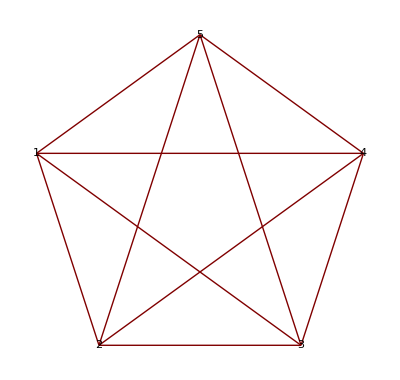
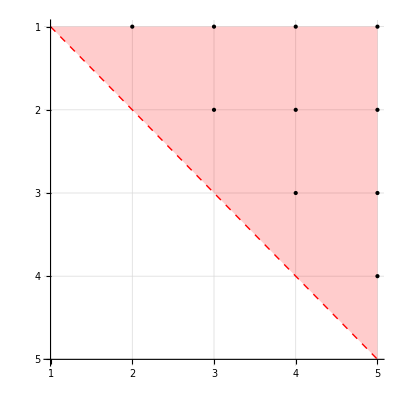

{1,2,3,4,5}

```mathematica
(* Simple Example: The initial ordering is ok! *)
G=Graph[{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5}];
{GraphPlot[G,VertexLabeling->True],PlotAdjacencyMatrix[G,True]}
i=BuildUpOrdering[G,{1,2,3,4}]
```

```mathematica
(* Harder Example: The initial ordering is not valid *)
```

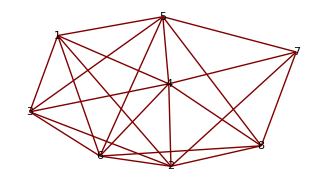
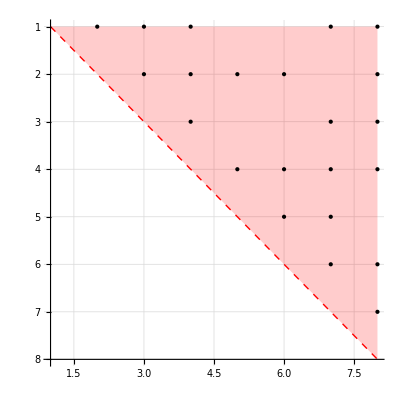

nFixedNeighs={∞,∞,∞,∞,0,0,0,0}

atomsToBeFixed={1,2,3,4}

Fixing: 1

atomOrder={1,0,0,0,0,0,0,0}

neighs={2,3,4,7,8}

nFixedNeighs={∞,∞,∞,∞,0,0,1,1}

atomsToBeFixed={2,3,4}

Fixing: 2

atomOrder={1,2,0,0,0,0,0,0}

neighs={1,3,4,8,5,6}

nFixedNeighs={∞,∞,∞,∞,1,1,1,2}

atomsToBeFixed={3,4}

Fixing: 3

atomOrder={1,2,3,0,0,0,0,0}

neighs={1,2,4,7,8}

nFixedNeighs={∞,∞,∞,∞,1,1,2,3}

atomsToBeFixed={4}

Fixing: 4

atomOrder={1,2,3,4,0,0,0,0}

neighs={1,2,3,7,8,5,6}

nFixedNeighs={∞,∞,∞,∞,2,2,3,4}

atomsToBeFixed={8}

Fixing: 8

atomOrder={1,2,3,4,0,0,0,5}

neighs={1,2,3,4,7,6}

nFixedNeighs={∞,∞,∞,∞,2,3,4,4}

atomsToBeFixed={7}

Fixing: 7

atomOrder={1,2,3,4,0,0,6,5}

neighs={1,3,4,8,5,6}

nFixedNeighs={∞,∞,∞,∞,3,4,4,5}

atomsToBeFixed={6}

Fixing: 6

atomOrder={1,2,3,4,0,7,6,5}

neighs={2,4,7,8,5}

nFixedNeighs={∞,∞,∞,∞,4,4,5,6}

atomsToBeFixed={5}

Fixing: 5

atomOrder={1,2,3,4,8,7,6,5}

neighs={2,4,7,6}

{1,2,3,4,8,7,6,5}

```mathematica
edges={1<->2,1<->3,1<->4,1<->7,1<->8,2<->3,2<->4,2<->5,2<->6,2<->8,3<->4,3<->7,3<->8,4<->6,4<->7,4<->8,4<->5,5<->6,5<->7,6<->7,6<->8,7<->8};
G=Graph[edges];
{GraphPlot[G,VertexLabeling->True],PlotAdjacencyMatrix[G,True]}
i=BuildUpOrdering[G,{1,2,3,4},True]
```

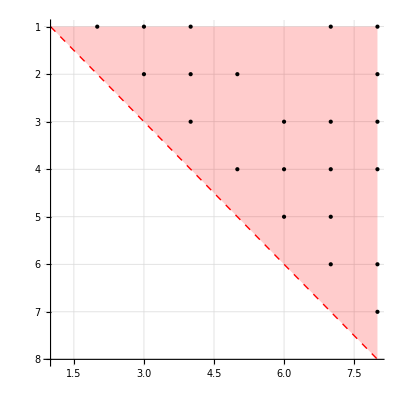
```mathematica
{-Graphics-,-Graphics-}
```

nFixedNeighs={∞,∞,∞,∞,0,0,0,0}

atomsToBeFixed={1,2,3,4}

Fixing: 1

atomOrder={1,0,0,0,0,0,0,0}

neighs={2,3,4,7,8}

nFixedNeighs={∞,∞,∞,∞,0,0,1,1}

atomsToBeFixed={2,3,4}

Fixing: 2

atomOrder={1,2,0,0,0,0,0,0}

neighs={1,3,4,8,5}

nFixedNeighs={∞,∞,∞,∞,1,0,1,2}

atomsToBeFixed={3,4}

Fixing: 3

atomOrder={1,2,3,0,0,0,0,0}

neighs={1,2,4,7,8,6}

nFixedNeighs={∞,∞,∞,∞,1,1,2,3}

atomsToBeFixed={4}

Fixing: 4

atomOrder={1,2,3,4,0,0,0,0}

neighs={1,2,3,7,8,5,6}

nFixedNeighs={∞,∞,∞,∞,2,2,3,4}

atomsToBeFixed={8}

Fixing: 8

atomOrder={1,2,3,4,0,0,0,5}

neighs={1,2,3,4,7,6}

nFixedNeighs={∞,∞,∞,∞,2,3,4,4}

atomsToBeFixed={7}

Fixing: 7

atomOrder={1,2,3,4,0,0,6,5}

neighs={1,3,4,8,5,6}

nFixedNeighs={∞,∞,∞,∞,3,4,4,5}

atomsToBeFixed={6}

Fixing: 6

atomOrder={1,2,3,4,0,7,6,5}

neighs={3,4,7,8,5}

nFixedNeighs={∞,∞,∞,∞,4,4,5,6}

atomsToBeFixed={5}

Fixing: 5

atomOrder={1,2,3,4,8,7,6,5}

neighs={2,4,7,6}

{1,2,3,4,8,7,6,5}

#### Solving an instance using BuilUpSolver method

```mathematica
M=GenerateRandomMDGP[5,5,0];
X=M["X"];
G=M["G"];
S=BuildUpSolver[G];
Print["LDME=",LDME[G,S]]
S
Table[Norm[S[[i]]-S[[5]]]^2,{i,4}]
```

```mathematica
G
```

## GASolver

### Source Code

#### GASolver

```mathematica
ClearAll[GASolver]
GANextBasis[G_,F_,U_,verbose_:False]:=Module[
{i,u,P,basis},
For[i=1,i≤Length[U],i++,
u=U[[i]];
P=Intersection[AdjacencyList[G,u],F];
If[Length[P]≥4,
basis=Take[P,4];
Return[basis]];
];
Throw["BasisCouldNotBeFound"];
];

GASetPosition[G_,X_,S_,basis_]:=Module[
{i,d,r,w,A,B,C,D,x,y,z,s,u,Y},
Y=Table[{0,0,0},{i,Length[S]}];
(* get basis coords *)
{x,y,z,s}=Table[X[[basis[[j]]]],{j,4}];
For[i=1,i≤Length[S],i++,
u=S[[i]];
(* get distances *)
r=Table[GetEdgeWeight[G,u->basis[[j]]],{j,4}];
(* get factors *) 
w={Sum[x[[j]]^2,{j,3}]-r[[1]]^2,Sum[y[[j]]^2,{j,3}]-r[[2]]^2,Sum[z[[j]]^2,{j,3}]-r[[3]]^2,Sum[s[[j]]^2,{j,3}]-r[[4]]^2};
A=0.5*{(x[[2]]*y[[3]]-x[[3]]*y[[2]])*w[[3]]+(x[[3]]*z[[2]]-x[[2]]*z[[3]])*w[[2]]+(y[[2]]*z[[3]]-y[[3]]*z[[2]])*w[[1]],(x[[3]]*y[[1]]-x[[1]]*y[[3]])*w[[3]]+(x[[1]]*z[[3]]-x[[3]]*z[[1]])*w[[2]]+(y[[3]]*z[[1]]-y[[1]]*z[[3]])*w[[1]],(x[[1]]*y[[2]]-x[[2]]*y[[1]])*w[[3]]+(x[[2]]*z[[1]]-x[[1]]*z[[2]])*w[[2]]+(y[[1]]*z[[2]]-y[[2]]*z[[1]])*w[[1]]};
B={x[[2]]*y[[3]]-x[[2]]*z[[3]]-x[[3]]*y[[2]]+x[[3]]*z[[2]]+y[[2]]*z[[3]]-y[[3]]*z[[2]],x[[3]]*y[[1]]-x[[3]]*z[[1]]-x[[1]]*y[[3]]+x[[1]]*z[[3]]+y[[3]]*z[[1]]-y[[1]]*z[[3]],x[[1]]*y[[2]]-x[[1]]*z[[2]]-x[[2]]*y[[1]]+x[[2]]*z[[1]]+y[[1]]*z[[2]]-y[[2]]*z[[1]]};
C=0.5*{(x[[1]]-z[[1]])*w[[2]]-(x[[1]]-y[[1]])*w[[3]]-(y[[1]]-z[[1]])*w[[1]],(x[[2]]-z[[2]])*w[[2]]-(x[[2]]-y[[2]])*w[[3]]-(y[[2]]-z[[2]])*w[[1]],(x[[3]]-z[[3]])*w[[2]]-(x[[3]]-y[[3]])*w[[3]]-(y[[3]]-z[[3]])*w[[1]]};
d=x[[1]]*y[[2]]*z[[3]]-x[[1]]*y[[3]]*z[[2]]-x[[2]]*y[[1]]*z[[3]]+x[[2]]*y[[3]]*z[[1]]+x[[3]]*y[[1]]*z[[2]]-x[[3]]*y[[2]]*z[[1]];
D={C[[2]]*s[[3]]-C[[3]]*s[[2]]-0.5*B[[1]]*w[[4]]+A[[1]],C[[3]]*s[[1]]-C[[1]]*s[[3]]-0.5*B[[2]]*w[[4]]+A[[2]],C[[1]]*s[[2]]-C[[2]]*s[[1]]-0.5*B[[3]]*w[[4]]+A[[3]],-Dot[A,s]+0.5*d*w[[4]],-Dot[B,s]+d};
Y[[i]]={D[[1]],D[[2]],D[[3]]}/D[[5]]
];
Return[Y]
];

GASolver[G_,verbose_:False]:=Module[
{i,d,x,y,z,r,s,u,w,basis,A,B,C,D,F,S,X,U},
{X,F}=BuildUpInitX[G,verbose];
U=Complement[Table[i,{i,Length[VertexList[G]]}],F];
(*set the remaining atoms*)
While[Length[U]>0,
basis=GANextBasis[G,F,U,verbose];
(* find atoms to set position *)
S=Intersection[AdjacencyList[G,basis[[1]]],U];
S=Intersection[AdjacencyList[G,basis[[2]]],S];
S=Intersection[AdjacencyList[G,basis[[3]]],S];
S=Intersection[AdjacencyList[G,basis[[4]]],S];
If[verbose,Print["F=",F," U=",U," basis=",basis," S=",S]];
X[[S]]=GASetPosition[G,X,S,basis];
F=Union[F,S];
U=Complement[U,S]
];
Return[X]
];
```

#### GASolver2 (Not working)

```mathematica
(*GASolver2[G_]:=Module[
{i,j,d,x,y,z,s,numberOfAtoms,A,C,B,D,Y,M,X,S,U2,U3,U4,V3,V4},
numberOfAtoms=Length[VertexList[G]];
X=Table[{0,0,0},{i,numberOfAtoms}];
(* set the position of the first four atoms *)
X[[2]][[1]]=GetEdgeWeight[G,1->2];U2=X[[2]][[1]];
X[[3]][[1]]=(GetEdgeWeight[G,3->1]^2-GetEdgeWeight[G,3->2]^2+U2^2)/(2*U2);U3=X[[3]][[1]];
X[[3]][[2]]=Sqrt[GetEdgeWeight[G,3->1]^2-U3^2];V3=X[[3]][[2]];
X[[4]][[1]]=(GetEdgeWeight[G,4->1]^2-GetEdgeWeight[G,4->2]^2+U2^2)/(2*U2);U4=X[[4]][[1]];
X[[4]][[2]]=(GetEdgeWeight[G,4->2]^2-GetEdgeWeight[G,4->3]^2-(U4-U2)^2+(U4-U3)^2+V3^2)/(2*V3);V4=X[[4]][[2]];
X[[4]][[3]]=Sqrt[GetEdgeWeight[G,4->1]^2-U4^2-V4^2];
(* set the remaining atoms *)
For[i=5,i≤numberOfAtoms,i++,
P=Select[AdjacencyList[G,i],#<i&];
If[Length[P]<4,Throw["NotEnoughAdjacentNodes"]];
Y=Table[X[[P[[j]]]],{j,4}];
S=Y[[4]];
(* squared distances *)
z=Table[Norm[Y[[j]]]^2-GetEdgeWeight[G,i->P[[j]]]^2,{j,4}];
M=Transpose[{Cross[Y[[2]],Y[[3]]],Cross[Y[[3]],Y[[1]]],Cross[Y[[2]],Y[[1]]]}];
A=0.5*(M.z[[1;;3]]);
B=Table[Sum[M[[k,j]],{j,3}],{k,3}];
C=0.5*(Transpose[{Y[[3]]-Y[[2]],Y[[1]]-Y[[3]],Y[[2]]-Y[[1]]}].z[[1;;3]]);
d =Det[Y[[1;;3]]];Print["Det(A)=",d];
D={C[[2]]*S[[3]]-C[[3]]*S[[2]]-B[[1]]*z[[4]]/2+A[[1]],
C[[3]]*S[[1]]-C[[1]]*S[[3]]-B[[2]]*z[[4]]/2+A[[2]],
C[[1]]*S[[2]]-C[[2]]*S[[1]]-B[[3]]*z[[4]]/2+A[[3]],
-Dot[A,S]+d*z[[4]]/2,
-Dot[B,S]+d};
X[[i]]={D[[1]],D[[2]],D[[3]]}/D[[5]];
];
Return[X]
];*)
```

### Example

```mathematica
M=GenerateRandomMDGP[150,5,"DistanceMatrix",0];
X=M["X"];
G=M["G"];
S=GASolver[G,False];
Print["LDME=",LDME[G,S]]
```

## Comparisons

### Speed

```mathematica
M=GenerateRandomMDGP[350,5,"DistanceMatrix",0];
G=M["G"];
Print["GA      = ",Timing[S=GASolver[G,False];]]
Print["BuildUp = ",Timing[Y=BuildUpSolver[G,False];]]
Print["LDME(GA)      = ",LDME[G,S]]
Print["LDME(BuildUp) = ",LDME[G,Y]]
```

### Robustness

#### Example: Colinear Points

```mathematica
(*z=Table[10^(i),{i,1,16}];
a=Table[0,{i,Length[z]}];
b=Table[0,{i,Length[z]}];
For[k=1,k≤Length[z],k++,
X={{0,0,0},{1,0,0},{0.5,1/z[[k]],0},{1,2,3}};
(* build graph *)
edges={};
weights={};
For[i=1,i≤4,i++,
For[j=i+1,j≤4,j++,
AppendTo[edges,i<->j];
AppendTo[weights,Norm[X[[i]]-X[[j]]]]
];
];
G=Graph[edges,EdgeWeight->weights];
Z=BPGetNodePosition[G,X,4,{1,1,1,1}];
Print["k= ",k,"  Log10[E]= ", Log10[Norm[X[[4]]-Z]] ]
];*)
```

#### Example B

```mathematica
z=Table[10^(-i),{i,0,12}];
a=Table[0,{i,Length[z]}];
b=Table[0,{i,Length[z]}];
For[k=1,k≤Length[z],k++,
X={{0,0,0},{1,0,0},{0,1,0},{1,1,z[[k]]},{.5,.5,1}};
(* build graph *)
edges={};
weights={};
For[i=1,i≤5,i++,
For[j=i+1,j≤5,j++,
AppendTo[edges,i<->j];
AppendTo[weights,Norm[X[[i]]-X[[j]]]]
];
];
G=Graph[edges,EdgeWeight->weights];
S={5};
basis={1,2,3,4};
a[[k]]=Norm[X[[S]]-BuildUpSetPosition[G,X,S,basis]];
b[[k]]=Norm[X[[S]]-GASetPosition[G,X,S,basis]]
];
```

## Articles:

### MMAS' 17

#### Problem

```mathematica
vertices={1,2,3,4,5,6};
(* create edges *)
edges={};
For[j=1,j≤3,j++,
For[k=1,k≤(Length[vertices]-j),k++,AppendTo[edges,k<->(k+j)]]
];
(* extra distances *)
AppendTo[edges,1<->5];
(* create graph *)
G=Graph[vertices,edges];
(* set edges values *)
For[k=1,k≤(Length[vertices]-1),k++,
PropertyValue[{G,k<->(k+1)},EdgeWeight]=1;
PropertyValue[{G,k<->(k+1)},"DistanceBounds"]={1,1}
]
For[k=1,k≤(Length[vertices]-2),k++,
PropertyValue[{G,k<->(k+2)},EdgeWeight]=Sqrt[3];
PropertyValue[{G,k<->(k+2)},"DistanceBounds"]={Sqrt[3],Sqrt[3]}
]
PropertyValue[{G,1<->4},EdgeWeight]=2.15;
PropertyValue[{G,1<->4},"DistanceBounds"]={2.15,2.15};
PropertyValue[{G,1<->5},EdgeWeight]=0;
PropertyValue[{G,1<->5},"DistanceBounds"]={2.45,2.55};
PropertyValue[{G,2<->5},EdgeWeight]=0;
PropertyValue[{G,2<->5},"DistanceBounds"]={2.2,2.6};
PropertyValue[{G,3<->6},EdgeWeight]=0;
PropertyValue[{G,3<->6},"DistanceBounds"]={2.4,2.6};
Print["G=",G]
Print["EdgesList[G]=",EdgeList[G]]
```

#### Getting Reference Solution

```mathematica
(* Create BP instance by removing the edge 1<->5 and choosing the lower bounds *)
H=EdgeDelete[G,1<->5];
PropertyValue[{H,2<->5},EdgeWeight]=PropertyValue[{H,2<->5},"DistanceBounds"][[1]];
PropertyValue[{H,3<->6},EdgeWeight]=PropertyValue[{H,3<->6},"DistanceBounds"][[1]];
Print["H=",H]
Print["EdgesList[H]=",EdgeList[H]]
(* solving *)
{S,work}=BPSolver[H];
XL=S["Points"];
BL=S["Branches"];
```

```mathematica
(* Create BP instance from H and choosing the upper bounds *)
PropertyValue[{H,2<->5},EdgeWeight]=PropertyValue[{H,2<->5},"DistanceBounds"][[2]];
PropertyValue[{H,3<->6},EdgeWeight]=PropertyValue[{H,3<->6},"DistanceBounds"][[2]];
(* solving *)
{S,work}=BPSolver[H];
XU=S["Points"];
BU=S["Branches"];
```

```mathematica
For[i=1,i≤Length[XL],i++,
Print[{i,XL[[i]][[5]],BL[[i]]}]
]
```

```mathematica
For[i=1,i≤Length[XU],i++,
Print[{i,XU[[i]][[5]],BU[[i]]}]
]
```

```mathematica
ω0=CalculateTorsionAngles[XL[[3]]]
```

```mathematica
ω1=CalculateTorsionAngles[XU[[3]]]
```

```mathematica
X=XL[[1]];
Y=ApplyRotors[X,{0,0,0,0,0.56,0}]
MatrixForm[DistanceMatrix[X]]
MatrixForm[DistanceMatrix[Y]]
ω5={0.56,0.62,0.733};
Y=Table[ApplyRotors[X,{0,0,0,0,ω5[[i]],0}],{i,Length[ω5]}];
Z=ApplyRotors[X,{0,0,0,0,0.68,0}];
figs=Table[{Line[Y[[i]]],{PointSize[.025],LightGray,Point[Y[[i]]]}},{i,Length[Y]}];
figs=Prepend[figs,{Line[Z],{PointSize[.025],Black,Point[Z]}}];
Graphics3D[figs, Axes->False]
```

```mathematica
ω6={0.56,0.62,0.68,0.733};
Y=Table[ApplyRotors[X,{0,0,0,0,0.68,ω6[[i]]}],{i,Length[ω6]}];
figs=Prepend[figs,Table[{Line[Y[[i]]],{PointSize[.025],LightGray,Point[Y[[i]]]}},{i,Length[Y]}]];
Graphics3D[figs, Axes->False]
```

-Graphics3D-